```mathematica
filename="examplePoints";
epsilon=0.01;
```

```mathematica
data=Import["~/uu/patternrecognition/RANSAC/data/"<>filename<>".csv"];
```

```mathematica
dataPlot=ListPlot[Partition[data,20],PlotRange->{{0,1},{0,1}},AspectRatio->1];
```

```mathematica
results=Import["~/uu/patternrecognition/RANSAC/data/"<>filename<>"_result.csv"];
```

```mathematica
results
```

{{0.495022,0.630664,0.201972,15},{0.313892,0.215736,0.135125,16},{0.587782,0.738357,0.257197,14},{0.54725,0.463861,0.262293,12},{0.418034,0.422131,0.306899,13}}

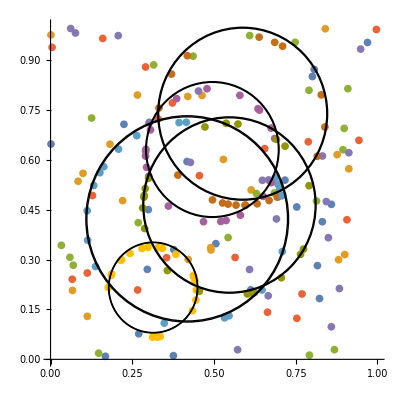

```mathematica
Show[dataPlot,{Circle[{#[[1]],#[[2]]},#[[3]]],Circle[{#[[1]],#[[2]]},#[[3]]*(1+epsilon)]}&/@results//Graphics]
```